```mathematica
Z=Exp[-β*ϵ]*(1+Exp[-β*δ])
```

ⅇ^(-β ϵ) (1+ⅇ^(-β δ))

```mathematica
-D[Log[Z],β]//FullSimplify
```

δ/(1+ⅇ^(β δ))+ϵ

```mathematica
D[-D[Log[Z],β]/.{β->1/(k*T)},T]//FullSimplify
```

(δ^2 Sech[δ/(2 k T)]^2)/(4 k T^2)

```mathematica
Integrate[ρ*D[-D[Log[Z],β]/.{β->1/(k*T)},T],{δ,0,Δ}]//FullSimplify
```

ConditionalExpression[-1/6 k^2 π^2 T ρ+((1-1/(1+ⅇ^(Δ/(k T)))) Δ^2 ρ)/T-2 k Δ ρ Log[1+ⅇ^(Δ/(k T))]-2 k^2 T ρ PolyLog[2,-ⅇ^(Δ/(k T))], ⅇ^(Δ/(k T))≥-1]

```mathematica
Integrate[ρ*D[-D[Log[Z],β]/.{β->1/(k*T)},T],{δ,0,Δ}]//FullSimplify//TeXForm
```

\fbox{$-2 k^2 \rho  T \text{Li}_2\left(-e^{\frac{\Delta }{k T}}\right)-\frac{1}{6} \pi
   ^2 k^2 \rho  T+\frac{\Delta ^2 \rho  \left(1-\frac{1}{e^{\frac{\Delta }{k
   T}}+1}\right)}{T}-2 \Delta  k \rho  \log \left(e^{\frac{\Delta }{k T}}+1\right)\text{
   if }e^{\frac{\Delta }{k T}}\geq -1$}

```mathematica
Limit[-1/6 k^2 π^2 T ρ+((1-1/(1+ⅇ^(Δ/(k T)))) Δ^2 ρ)/T-2 k Δ ρ Log[1+ⅇ^(Δ/(k T))]-2 k^2 T ρ PolyLog[2,-ⅇ^(Δ/(k T))],T->0]
```

ConditionalExpression[0, ρ∈ℝ&&k Δ>0]

```mathematica
Limit[-1/6 k^2 π^2 T ρ+((1-1/(1+ⅇ^(Δ/(k T)))) Δ^2 ρ)/T-2 k Δ ρ Log[1+ⅇ^(Δ/(k T))]-2 k^2 T ρ PolyLog[2,-ⅇ^(Δ/(k T))],T->Infinity]
```

0

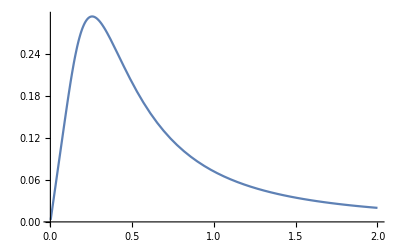

```mathematica
Plot[-1/6  π^2 T +(1-1/(1+ⅇ^(1/T)))/T-2 Log[1+ⅇ^(1/T)]-2 T  PolyLog[2,-ⅇ^(1/T)],{T,0.001,2}]
```